# Problem Set 15

## Section 37

```mathematica
If[EvenQ[#],Style[#,Background->Yellow],Style[#,Background->LightGray]]&/@Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
If[PrimeQ[#],Framed[#],#]&/@Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
If[PrimeQ[#],Labeled[Framed[#],Style[Mod[#,4],LightGray]],#]&/@Range[100]
```

{1,22,33,4,51,6,73,8,9,10,113,12,131,14,15,16,171,18,193,20,21,22,233,24,25,26,27,28,291,30,313,32,33,34,35,36,371,38,39,40,411,42,433,44,45,46,473,48,49,50,51,52,531,54,55,56,57,58,593,60,611,62,63,64,65,66,673,68,69,70,713,72,731,74,75,76,77,78,793,80,81,82,833,84,85,86,87,88,891,90,91,92,93,94,95,96,971,98,99,100}

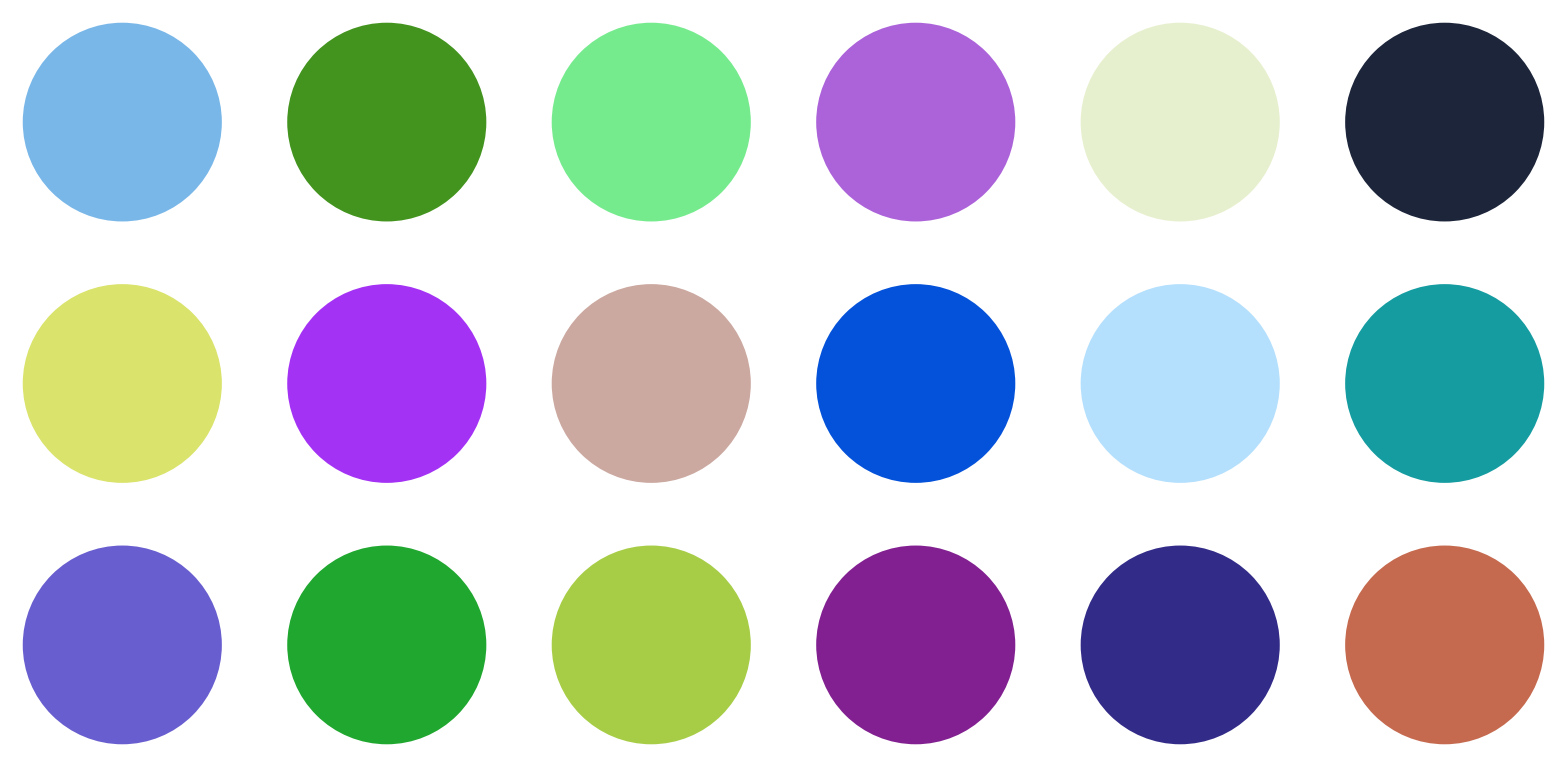

```mathematica
GraphicsGrid[Table[Graphics[Style[Disk[],RandomColor[]]],3,6]]
```

```mathematica
PieChart[Labeled[EntityValue[#,"GDP"],EntityValue[#,"Name"]]&/@EntityList[],{}]
```

-Graphics-

```mathematica
PieChart[Legended[EntityValue[#,"Population"],EntityValue[#,"Name"]]&/@EntityList[],{}]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[PieChart[Length/@Gather[IntegerDigits[2^#]]]&/@Range[25],5]]
```

-Graphics-

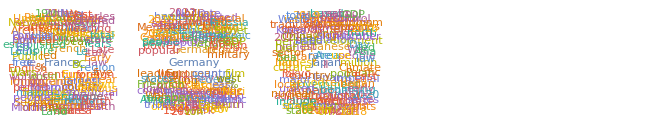

```mathematica
GraphicsRow[WordCloud[WikipediaData[#]]&/@EntityList[]]
```

## Section 38

```mathematica
Module[{x=Range[10]},x^2+x]
```

{2,6,12,20,30,42,56,72,90,110}

```mathematica
Module[{x=RandomInteger[100,10]},Column[{x,Sort[x],Max[x],Total[x]}]]
```

{100,99,94,90,39,52,1,50,41,67}
{1,39,41,50,52,67,90,94,99,100}
100
633

```mathematica
Module[{x=["Image"]},ImageCollage[{x,Blur[x],EdgeDetect[x],ColorNegate[x]}]]
```

-Graphics-

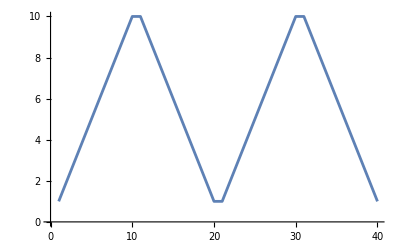

```mathematica
Module[{r=Range[10]},ListLinePlot[Join[r,Reverse[r],r,Reverse[r]]]]
```

```mathematica
Module[{x=Range[10]},{x+1,x-1,Reverse[x]}]
```

{{2,3,4,5,6,7,8,9,10,11},{0,1,2,3,4,5,6,7,8,9},{10,9,8,7,6,5,4,3,2,1}}

```mathematica
NestList[Mod[17#+2,11]&,10,20]
```

{10,7,0,2,3,9,1,8,6,5,10,7,0,2,3,9,1,8,6,5,10}

```mathematica
Module[{c,v},v={"a","e","i","o","u"}; c=If[MemberQ[v,#],Nothing,#]&/@Alphabet[];Table[StringJoin[{RandomChoice[c],RandomChoice[v],RandomChoice[c],RandomChoice[v],RandomChoice[c]}],10]]
```

{mecap,pacaf,qepak,boqum,gotip,zajuw,hisiw,qayax,jejez,pezuq}